## Bounds on EDGB Theory From the Overall Posterior of GW151226

```mathematica
(*Originially I did seperate calculations of randomly selected 1000 dataset from the posterior and also for overall posterior. We found that it was better to consider the overall data since the results based on randomly selected data weren't consistent. I decided to keep the results only from overall dataset. Thats why many of the names I gave to differnt functions have the word 'all' with it. I just decided to keep it that way *)
```

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post.csv","CSV"] ;(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-all-beta.csv","CSV"] ; (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-all-alpha.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
m1All=dataOverall1[[All,5]]*tsolar/.tsolar->4.925491*10^-6;
m2All=dataOverall1[[All,6]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1/1.64485*dataOverall2[[All,1]];(*1-sigma upper bound*)
αppEAll=1/1.64485*dataOverall3[[All,1]](*1-sigma upper bound*);
```

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] ;(*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

52252

```mathematica
Length[βppEAll]
```

52252

```mathematica
Mean[ζampAll]
```

12509.6

```mathematica
Mean[ζphaseAll]
```

360.999

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

51355

```mathematica
Length[ζAllampSelected]
```

46872

```mathematica
Mean[ζAllphaseSelected]
```

0.0174016

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.074786

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},{0.789122,472.033,1.76752,0.97753,11.7264,10.59,0.967842,0.949848,0.436653,-0.301389,0.04629,1.58619},52249,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] (*Data satisfying zeta_phase<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},{0.789122,472.033,1.76752,0.97753,11.7264,10.59,0.967842,0.949848,0.436653,-0.301389},51351,{0.280777,395.397,3.53078,-0.343669,14.3417,8.84549,0.719679,0.111302,0.429138,0.208536},{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},{0.860122,617.575,3.77383,-0.740918,14.4537,8.68031,0.407971,0.658073,0.00252138,0.838901,0.00149139,0.0522075},46869,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A4[[All,12]]
```

{0.0171763,0.0522075,0.165549,0.0378357,0.0127864,0.0533918,0.0167203,0.0161527,0.129926,0.00981887,0.47965,0.00759042,46848,0.639428,0.00528177,0.0983506,0.0425141,0.0196601,0.0140803,0.0231292,0.000514475,0.0374042,0.727602,0.0315771,0.0686092}
 |  |  |  |

```mathematica
Length[A3]
```

51355

```mathematica
Length[A4]
```

46872

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.094265

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{4.81405,13.8985,6.13673,8.01727,12.5915,5.6388,4.50492,6.70477,4.82258,4.70667,7.63853,4.61487,10.3065,4.16243,52224,3.94756,11.1,3.81312,7.08526,5.78595,19.394,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

{2.015,5.74447,2.52291,3.29495,5.19042,2.31966,1.90965,2.94321,2.04561,1.98368,3.14457,2.10142,4.26331,1.84368,52225,4.61358,1.71006,2.90948,2.38032,7.96884,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

7.87527

```mathematica
Mean[SqrtαEDGBphase]
```

3.31329

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

{2.015,2.52291,3.29495,2.31966,1.90965,2.94321,2.04561,1.98368,3.14457,2.10142,4.26331,1.84368,1.80758,1.89248,46845,1.73059,4.61358,1.71006,2.90948,2.38032,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

{4.81405,6.13673,8.01727,5.6388,4.50492,6.70477,4.82258,4.70667,7.63853,4.61487,10.3065,4.16243,4.1191,4.01867,46844,6.49683,3.94756,11.1,3.81312,7.08526,5.78595,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

# Bounds from Phase Correction Using Compound Probability:

```mathematica
fun1=1/(√(2*π*(ζphaseAll)^2))*Exp[-x^2/(2Exp[2 Log[ζphaseAll]])] (*x is \[Zeta. and ζphaseAll is sigma_zeta from Fisher analysis*)
```

{756.691 ⅇ^(-1.79882×10^6 x^2),8.61832 ⅇ^(-233.343 x^2),267.496 ⅇ^(-224795. x^2),52247,437.105 ⅇ^(-600234. x^2),205.799 ⅇ^(-133056. x^2)}
 |  |  |  |

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

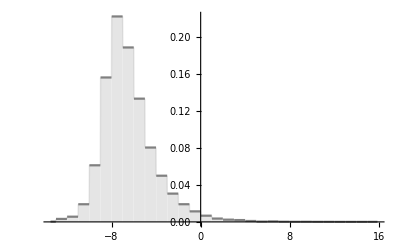

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

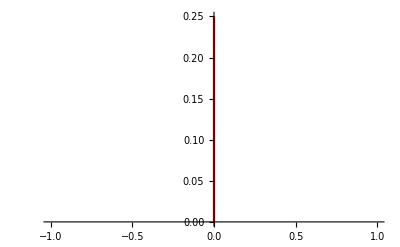

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red]
```

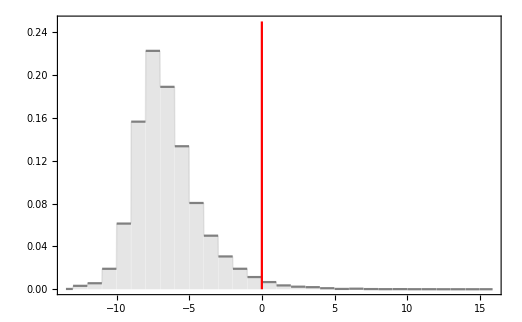

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] (*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Log[Max[ζphaseAll]]
```

15.8769

```mathematica
Log[Min[ζphaseAll]]
```

-13.4813

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.999836

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*98% area under the curve satisfies zeta<1 from phase correction*)
```

98.2835

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
Min[Log[ζampAll]]
```

-10.7176

```mathematica
Max[Log[ζampAll]]
```

19.4335

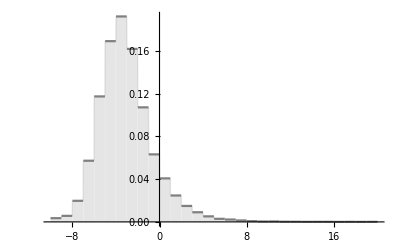

```mathematica
plottestamp=Plot[ps2amp[x],{x,-10,20},Filling->Axis,PlotStyle->Gray]
```

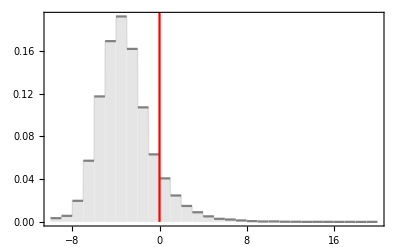

```mathematica
Show[plottestamp,zeta1,Frame->True]  (*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

89.7039

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.9998

```mathematica
fun2=PDF[𝒟log,Log[ζphaseAll]] (*pdf of log(sigma_zeta)|log_sigma_zeta*)
```

{0.222556,0.0500268,0.188969,0.133507,0.0500268,0.188969,0.222556,52238,0.222556,0.222556,0.0191189,0.188969,0.0500268,0.188969,0.188969}
 |  |  |  |

```mathematica
fun3=fun1*fun2
```

{168.406 ⅇ^(-1.79882×10^6 x^2),0.431147 ⅇ^(-233.343 x^2),50.5485 ⅇ^(-224795. x^2),52247,82.5992 ⅇ^(-600234. x^2),38.8896 ⅇ^(-133056. x^2)}
 |  |  |  |

```mathematica
(*Length[fun3]*)
```

```mathematica
(*fun4=fun3/.x->0.0000001*)
```

```mathematica
fun5=Transpose[{Log[ζphaseAll],fun3}]
```

{{-7.54789,168.406 ⅇ^(-1.79882×10^6 x^2)},{-3.07283,0.431147 ⅇ^(-233.343 x^2)},{-6.50804,50.5485 ⅇ^(-224795. x^2)},52246,{-3.86471,0.951776 ⅇ^(-1137.14 x^2)},{-6.99911,82.5992 ⅇ^(-600234. x^2)},{-6.24584,38.8896 ⅇ^(-133056. x^2)}}
 |  |  |  |

```mathematica
(*fun6=Interpolation[fun5]*)(*Unless we give a specific value of x, NIntegrate is not possible*)
```

```mathematica
(*NIntegrate[fun6[z],{z,0,1}]*)
```

```mathematica
ΔζphaseAll=Table[Abs[Log[ζphaseAll[[i+1]]]-Log[ζphaseAll[[i]]]],{i,1,Length[βppEAll]-1}] (* delta sigma_zeta *)
```

{4.47507,3.43522,1.15273,1.89889,3.37108,0.964872,1.56901,52237,0.0628702,0.236926,3.38505,3.73557,2.91202,3.1344,0.753273}
 |  |  |  |

```mathematica
fun7=Table[ΔζphaseAll[[i]]*fun3[[i]],{i,1,Length[ΔζphaseAll]}]
```

{753.629 ⅇ^(-1.79882×10^6 x^2),1.48108 ⅇ^(-233.343 x^2),58.2689 ⅇ^(-224795. x^2),52246,2.98325 ⅇ^(-1137.14 x^2),62.2197 ⅇ^(-600234. x^2)}
 |  |  |  |

```mathematica
fun8=Total[fun7] (*This is the pdf for zeta*)
```

1043.22 ⅇ^(-2.56248×10^11 x^2)+483.444 ⅇ^(-2.46016×10^11 x^2)+52247+4.83532×10^-11 ⅇ^(-8.85438×10^-15 x^2)+4.509×10^-11 ⅇ^(-8.09994×10^-15 x^2)
 |  |  |  |

```mathematica
(*fun8/.x->0.0000001*)
```

```mathematica
fun9[x_]=fun8
```

1043.22 ⅇ^(-2.56248×10^11 x^2)+483.444 ⅇ^(-2.46016×10^11 x^2)+52247+4.83532×10^-11 ⅇ^(-8.85438×10^-15 x^2)+4.509×10^-11 ⅇ^(-8.09994×10^-15 x^2)
 |  |  |  |

```mathematica
Sample= Table[10^-2*i,{i,-1000,1000}]//N;
```

```mathematica
points=Table[Sample[[i]],{i,1,2001}];(*These are the values of zeta that we are going to use for plotting the pdf of zeta. I am considering from -10 to 10 as suggested by you. But we don't know any good reason behind this except the fact that it is going to take more time if you go beyond this. Technincally, we are supposed to find the pdf upto 300, since it is mean of zeta from monte-carlo*)
```

```mathematica
pdfzeta=Map[fun9,points] (*This is going to take about five minutes.*)
```

General::munfl: Exp[-2.56248×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.46016×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45214×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.132748,0.132963,0.133179,0.133395,0.133612,0.13383,0.134048,0.134267,0.134486,0.134706,0.134926,0.135148,0.135369,0.135592,0.135815,0.136038,0.136263,0.136488,0.136713,0.136939,0.137166,0.137394,0.137622,0.137851,0.13808,0.13831,0.138541,0.138772,0.139004,0.139237,0.139471,0.139705,0.139939,0.140175,0.140411,0.140648,0.140885,0.141123,0.141362,0.141602,0.141842,0.142083,0.142324,0.142567,0.14281,0.143054,0.143298,0.143543,0.143789,0.144036,0.144283,0.144531,0.14478,0.14503,0.14528,0.145531,0.145783,0.146035,0.146288,0.146542,0.146797,0.147053,0.147309,0.147566,0.147824,0.148082,0.148342,0.148602,0.148863,0.149125,0.149387,0.14965,0.149914,0.150179,0.150445,0.150711,0.150979,0.151247,0.151516,0.151786,0.152056,0.152328,0.1526,0.152873,0.153147,0.153421,0.153697,0.153974,0.154251,0.154529,0.154808,0.155088,0.155369,0.15565,0.155933,0.156216,0.1565,0.156785,0.157071,0.157358,0.157646,0.157935,0.158224,0.158515,0.158806,0.159099,0.159392,0.159686,0.159981,0.160277,0.160574,0.160872,0.161171,0.161471,0.161772,0.162074,0.162376,0.16268,0.162985,0.163291,0.163597,0.163905,0.164213,0.164523,0.164834,0.165145,0.165458,0.165772,0.166086,0.166402,0.166719,0.167036,0.167355,0.167675,0.167996,0.168318,0.168641,0.168965,0.16929,0.169616,0.169944,0.170272,0.170601,0.170932,0.171264,0.171596,0.17193,0.172265,0.172601,0.172939,0.173277,0.173616,0.173957,0.174299,0.174642,0.174986,0.175331,0.175677,0.176025,0.176374,0.176724,0.177075,0.177427,0.177781,0.178136,0.178492,0.178849,0.179207,0.179567,0.179928,0.18029,0.180654,0.181018,0.181384,0.181751,0.18212,0.18249,0.182861,0.183233,0.183607,0.183982,0.184358,0.184736,0.185115,0.185495,0.185877,0.18626,0.186644,0.18703,0.187417,0.187805,0.188195,0.188586,0.188979,0.189373,0.189769,0.190166,0.190564,0.190964,0.191365,0.191768,0.192172,0.192577,0.192984,0.193393,0.193803,0.194214,0.194627,0.195042,0.195458,0.195876,0.196295,0.196716,0.197138,0.197562,0.197987,0.198414,0.198843,0.199273,0.199705,0.200138,0.200573,0.20101,0.201448,0.201888,0.20233,0.202773,0.203218,0.203665,0.204113,0.204563,0.205015,0.205468,0.205923,0.20638,0.206839,0.2073,0.207762,0.208226,0.208692,0.20916,0.209629,0.2101,0.210573,0.211048,0.211525,0.212004,0.212485,0.212967,0.213451,0.213938,0.214426,0.214916,0.215408,0.215902,0.216398,0.216896,0.217396,0.217898,0.218402,0.218908,0.219416,0.219926,0.220438,0.220953,0.221469,0.221987,0.222508,0.22303,0.223555,0.224082,0.224611,0.225142,0.225676,0.226212,0.226749,0.227289,0.227832,0.228376,0.228923,0.229472,0.230024,0.230577,0.231133,0.231692,0.232253,0.232816,0.233381,0.233949,0.234519,0.235092,0.235667,0.236245,0.236825,0.237407,0.237992,0.23858,0.23917,0.239763,0.240358,0.240955,0.241556,0.242159,0.242764,0.243373,0.243984,0.244597,0.245214,0.245833,0.246454,0.247079,0.247706,0.248336,0.248969,0.249605,0.250243,0.250884,0.251529,0.252176,0.252826,0.253479,0.254135,0.254793,0.255455,0.25612,0.256788,0.257459,0.258133,0.25881,0.25949,0.260174,0.26086,0.26155,0.262243,0.262939,0.263638,0.264341,0.265047,0.265756,0.266468,0.267184,0.267903,0.268626,0.269352,0.270081,0.270814,0.27155,0.27229,0.273034,0.273781,0.274531,0.275285,0.276043,0.276804,0.277569,0.278338,0.279111,0.279887,0.280667,0.281451,0.282239,0.28303,0.283826,0.284625,0.285428,0.286236,0.287047,0.287862,0.288682,0.289505,0.290332,0.291164,0.292,0.29284,0.293684,0.294533,0.295386,0.296243,0.297104,0.29797,0.298841,0.299715,0.300594,0.301478,0.302366,0.303259,0.304157,0.305059,0.305966,0.306877,0.307793,0.308714,0.30964,0.310571,0.311506,0.312446,0.313392,0.314342,0.315298,0.316258,0.317224,0.318194,0.31917,0.320151,0.321137,0.322129,0.323126,0.324128,0.325136,0.326149,0.327168,0.328192,0.329222,0.330257,0.331298,0.332345,0.333397,0.334455,0.335519,0.336589,0.337665,0.338747,0.339835,0.340929,0.342029,0.343135,0.344247,0.345365,0.34649,0.347621,0.348759,0.349903,0.351053,0.35221,0.353373,0.354543,0.35572,0.356904,0.358094,0.359291,0.360495,0.361706,0.362924,0.364149,0.365381,0.36662,0.367866,0.36912,0.370381,0.371649,0.372925,0.374209,0.375499,0.376798,0.378104,0.379418,0.380739,0.382069,0.383406,0.384752,0.386105,0.387466,0.388836,0.390214,0.3916,0.392995,0.394398,0.395809,0.397229,0.398658,0.400095,0.401541,0.402996,0.40446,0.405932,0.407414,0.408905,0.410405,0.411915,0.413433,0.414961,0.416499,0.418046,0.419603,0.421169,0.422746,0.424332,0.425928,0.427534,0.42915,0.430777,0.432414,0.434061,0.435718,0.437386,0.439065,0.440754,0.442454,0.444165,0.445887,0.44762,0.449365,0.45112,0.452887,0.454665,0.456455,0.458256,0.460069,0.461893,0.46373,0.465579,0.467439,0.469312,0.471197,0.473095,0.475005,0.476928,0.478863,0.480811,0.482772,0.484746,0.486733,0.488733,0.490747,0.492774,0.494815,0.496869,0.498938,0.50102,0.503116,0.505226,0.50735,0.509489,0.511642,0.51381,0.515993,0.518191,0.520403,0.522631,0.524874,0.527132,0.529405,0.531695,0.534,0.536321,0.538658,0.541011,0.54338,0.545766,0.548168,0.550588,0.553024,0.555477,0.557947,0.560434,0.562939,0.565461,0.568001,0.570559,0.573135,0.57573,0.578342,0.580973,0.583623,0.586292,0.588979,0.591686,0.594412,0.597157,0.599923,0.602708,0.605512,0.608338,0.611183,0.614049,0.616936,0.619843,0.622772,0.625722,0.628693,0.631686,0.6347,0.637737,0.640796,0.643877,0.646981,0.650108,0.653257,0.65643,0.659626,0.662846,0.666089,0.669357,0.672649,0.675965,0.679306,0.682672,0.686062,0.689479,0.69292,0.696388,0.699882,0.703401,0.706948,0.710521,0.714121,0.717748,0.721403,0.725085,0.728796,0.732535,0.736302,0.740098,0.743923,0.747777,0.751661,0.755574,0.759518,0.763492,0.767497,0.771533,0.7756,0.779698,0.783829,0.787991,0.792186,0.796414,0.800675,0.804969,0.809297,0.813659,0.818055,0.822486,0.826952,0.831453,0.83599,0.840563,0.845172,0.849818,0.854501,0.859222,0.863981,0.868777,0.873613,0.878487,0.883401,0.888354,0.893348,0.898382,0.903457,0.908573,0.913732,0.918932,0.924176,0.929462,0.934792,0.940166,0.945584,0.951048,0.956556,0.962111,0.967712,0.97336,0.979055,0.984798,0.99059,0.99643,1.00232,1.00826,1.01425,1.02029,1.02638,1.03253,1.03873,1.04498,1.05128,1.05764,1.06406,1.07053,1.07706,1.08364,1.09028,1.09698,1.10374,1.11056,1.11744,1.12438,1.13139,1.13845,1.14558,1.15278,1.16004,1.16736,1.17475,1.18221,1.18973,1.19733,1.205,1.21273,1.22054,1.22842,1.23637,1.2444,1.25251,1.26069,1.26894,1.27728,1.2857,1.29419,1.30277,1.31143,1.32018,1.329,1.33792,1.34692,1.35601,1.36519,1.37447,1.38383,1.39329,1.40284,1.41249,1.42223,1.43208,1.44202,1.45207,1.46222,1.47248,1.48284,1.49331,1.50389,1.51458,1.52538,1.5363,1.54734,1.55849,1.56976,1.58116,1.59268,1.60432,1.61609,1.628,1.64003,1.6522,1.6645,1.67695,1.68953,1.70226,1.71513,1.72815,1.74132,1.75464,1.76812,1.78176,1.79555,1.80952,1.82364,1.83794,1.85241,1.86705,1.88187,1.89687,1.91206,1.92743,1.943,1.95876,1.97472,1.99088,2.00724,2.02382,2.0406,2.05761,2.07483,2.09228,2.10996,2.12787,2.14603,2.16442,2.18306,2.20195,2.2211,2.24051,2.26019,2.28013,2.30036,2.32087,2.34166,2.36275,2.38414,2.40584,2.42784,2.45017,2.47282,2.49579,2.51911,2.54277,2.56678,2.59115,2.61589,2.641,2.66649,2.69236,2.71864,2.74532,2.77241,2.79993,2.82787,2.85626,2.8851,2.91439,2.94415,2.97439,3.00512,3.03635,3.06809,3.10035,3.13315,3.16648,3.20037,3.23483,3.26987,3.30551,3.34174,3.3786,3.41609,3.45423,3.49302,3.5325,3.57266,3.61353,3.65513,3.69746,3.74055,3.78441,3.82906,3.87452,3.92081,3.96794,4.01594,4.06483,4.11462,4.16534,4.21701,4.26966,4.3233,4.37796,4.43366,4.49043,4.5483,4.60729,4.66743,4.72875,4.79127,4.85504,4.92007,4.9864,5.05407,5.12311,5.19356,5.26544,5.33881,5.41369,5.49014,5.56819,5.64789,5.72927,5.8124,5.89732,5.98408,6.07273,6.16333,6.25594,6.35061,6.44741,6.54641,6.64766,6.75125,6.85724,6.96572,7.07676,7.19045,7.30688,7.42613,7.54831,7.67352,7.80186,7.93344,8.06839,8.20681,8.34885,8.49464,8.64432,8.79803,8.95593,9.1182,9.28499,9.4565,9.63291,9.81443,10.0013,10.1936,10.3918,10.5959,10.8064,11.0234,11.2472,11.4782,11.7167,11.963,12.2174,12.4804,12.7523,13.0336,13.3246,13.6259,13.938,14.2613,14.5965,14.944,15.3045,15.6787,16.0672,16.4708,16.8902,17.3262,17.7797,18.2516,18.7429,19.2545,19.7876,20.3433,20.9229,21.5276,22.1588,22.8181,23.507,24.2272,24.9805,25.7688,26.5942,27.459,28.3655,29.3164,30.3143,31.3623,32.4636,33.6218,34.8406,36.1243,37.4774,38.9049,40.4122,42.0055,43.6913,45.477,47.3709,49.3823,51.5213,53.7995,56.2302,58.8279,61.6096,64.5944,67.8041,71.264,75.0026,79.0533,83.4542,88.2496,93.4908,99.2373,105.558,112.535,120.263,128.852,138.434,149.166,161.232,174.855,190.302,207.902,228.055,251.265,278.171,309.61,346.699,390.985,444.669,510.974,594.745,703.405,848.533,1048.48,1333.06,1753.81,2412.2,3548.84,5836.27,11613.8,38815.2,1.53605×10^7,38815.2,11613.8,5836.27,3548.84,2412.2,1753.81,1333.06,1048.48,848.533,703.405,594.745,510.974,444.669,390.985,346.699,309.61,278.171,251.265,228.055,207.902,190.302,174.855,161.232,149.166,138.434,128.852,120.263,112.535,105.558,99.2373,93.4908,88.2496,83.4542,79.0533,75.0026,71.264,67.8041,64.5944,61.6096,58.8279,56.2302,53.7995,51.5213,49.3823,47.3709,45.477,43.6913,42.0055,40.4122,38.9049,37.4774,36.1243,34.8406,33.6218,32.4636,31.3623,30.3143,29.3164,28.3655,27.459,26.5942,25.7688,24.9805,24.2272,23.507,22.8181,22.1588,21.5276,20.9229,20.3433,19.7876,19.2545,18.7429,18.2516,17.7797,17.3262,16.8902,16.4708,16.0672,15.6787,15.3045,14.944,14.5965,14.2613,13.938,13.6259,13.3246,13.0336,12.7523,12.4804,12.2174,11.963,11.7167,11.4782,11.2472,11.0234,10.8064,10.5959,10.3918,10.1936,10.0013,9.81443,9.63291,9.4565,9.28499,9.1182,8.95593,8.79803,8.64432,8.49464,8.34885,8.20681,8.06839,7.93344,7.80186,7.67352,7.54831,7.42613,7.30688,7.19045,7.07676,6.96572,6.85724,6.75125,6.64766,6.54641,6.44741,6.35061,6.25594,6.16333,6.07273,5.98408,5.89732,5.8124,5.72927,5.64789,5.56819,5.49014,5.41369,5.33881,5.26544,5.19356,5.12311,5.05407,4.9864,4.92007,4.85504,4.79127,4.72875,4.66743,4.60729,4.5483,4.49043,4.43366,4.37796,4.3233,4.26966,4.21701,4.16534,4.11462,4.06483,4.01594,3.96794,3.92081,3.87452,3.82906,3.78441,3.74055,3.69746,3.65513,3.61353,3.57266,3.5325,3.49302,3.45423,3.41609,3.3786,3.34174,3.30551,3.26987,3.23483,3.20037,3.16648,3.13315,3.10035,3.06809,3.03635,3.00512,2.97439,2.94415,2.91439,2.8851,2.85626,2.82787,2.79993,2.77241,2.74532,2.71864,2.69236,2.66649,2.641,2.61589,2.59115,2.56678,2.54277,2.51911,2.49579,2.47282,2.45017,2.42784,2.40584,2.38414,2.36275,2.34166,2.32087,2.30036,2.28013,2.26019,2.24051,2.2211,2.20195,2.18306,2.16442,2.14603,2.12787,2.10996,2.09228,2.07483,2.05761,2.0406,2.02382,2.00724,1.99088,1.97472,1.95876,1.943,1.92743,1.91206,1.89687,1.88187,1.86705,1.85241,1.83794,1.82364,1.80952,1.79555,1.78176,1.76812,1.75464,1.74132,1.72815,1.71513,1.70226,1.68953,1.67695,1.6645,1.6522,1.64003,1.628,1.61609,1.60432,1.59268,1.58116,1.56976,1.55849,1.54734,1.5363,1.52538,1.51458,1.50389,1.49331,1.48284,1.47248,1.46222,1.45207,1.44202,1.43208,1.42223,1.41249,1.40284,1.39329,1.38383,1.37447,1.36519,1.35601,1.34692,1.33792,1.329,1.32018,1.31143,1.30277,1.29419,1.2857,1.27728,1.26894,1.26069,1.25251,1.2444,1.23637,1.22842,1.22054,1.21273,1.205,1.19733,1.18973,1.18221,1.17475,1.16736,1.16004,1.15278,1.14558,1.13845,1.13139,1.12438,1.11744,1.11056,1.10374,1.09698,1.09028,1.08364,1.07706,1.07053,1.06406,1.05764,1.05128,1.04498,1.03873,1.03253,1.02638,1.02029,1.01425,1.00826,1.00232,0.99643,0.99059,0.984798,0.979055,0.97336,0.967712,0.962111,0.956556,0.951048,0.945584,0.940166,0.934792,0.929462,0.924176,0.918932,0.913732,0.908573,0.903457,0.898382,0.893348,0.888354,0.883401,0.878487,0.873613,0.868777,0.863981,0.859222,0.854501,0.849818,0.845172,0.840563,0.83599,0.831453,0.826952,0.822486,0.818055,0.813659,0.809297,0.804969,0.800675,0.796414,0.792186,0.787991,0.783829,0.779698,0.7756,0.771533,0.767497,0.763492,0.759518,0.755574,0.751661,0.747777,0.743923,0.740098,0.736302,0.732535,0.728796,0.725085,0.721403,0.717748,0.714121,0.710521,0.706948,0.703401,0.699882,0.696388,0.69292,0.689479,0.686062,0.682672,0.679306,0.675965,0.672649,0.669357,0.666089,0.662846,0.659626,0.65643,0.653257,0.650108,0.646981,0.643877,0.640796,0.637737,0.6347,0.631686,0.628693,0.625722,0.622772,0.619843,0.616936,0.614049,0.611183,0.608338,0.605512,0.602708,0.599923,0.597157,0.594412,0.591686,0.588979,0.586292,0.583623,0.580973,0.578342,0.57573,0.573135,0.570559,0.568001,0.565461,0.562939,0.560434,0.557947,0.555477,0.553024,0.550588,0.548168,0.545766,0.54338,0.541011,0.538658,0.536321,0.534,0.531695,0.529405,0.527132,0.524874,0.522631,0.520403,0.518191,0.515993,0.51381,0.511642,0.509489,0.50735,0.505226,0.503116,0.50102,0.498938,0.496869,0.494815,0.492774,0.490747,0.488733,0.486733,0.484746,0.482772,0.480811,0.478863,0.476928,0.475005,0.473095,0.471197,0.469312,0.467439,0.465579,0.46373,0.461893,0.460069,0.458256,0.456455,0.454665,0.452887,0.45112,0.449365,0.44762,0.445887,0.444165,0.442454,0.440754,0.439065,0.437386,0.435718,0.434061,0.432414,0.430777,0.42915,0.427534,0.425928,0.424332,0.422746,0.421169,0.419603,0.418046,0.416499,0.414961,0.413433,0.411915,0.410405,0.408905,0.407414,0.405932,0.40446,0.402996,0.401541,0.400095,0.398658,0.397229,0.395809,0.394398,0.392995,0.3916,0.390214,0.388836,0.387466,0.386105,0.384752,0.383406,0.382069,0.380739,0.379418,0.378104,0.376798,0.375499,0.374209,0.372925,0.371649,0.370381,0.36912,0.367866,0.36662,0.365381,0.364149,0.362924,0.361706,0.360495,0.359291,0.358094,0.356904,0.35572,0.354543,0.353373,0.35221,0.351053,0.349903,0.348759,0.347621,0.34649,0.345365,0.344247,0.343135,0.342029,0.340929,0.339835,0.338747,0.337665,0.336589,0.335519,0.334455,0.333397,0.332345,0.331298,0.330257,0.329222,0.328192,0.327168,0.326149,0.325136,0.324128,0.323126,0.322129,0.321137,0.320151,0.31917,0.318194,0.317224,0.316258,0.315298,0.314342,0.313392,0.312446,0.311506,0.310571,0.30964,0.308714,0.307793,0.306877,0.305966,0.305059,0.304157,0.303259,0.302366,0.301478,0.300594,0.299715,0.298841,0.29797,0.297104,0.296243,0.295386,0.294533,0.293684,0.29284,0.292,0.291164,0.290332,0.289505,0.288682,0.287862,0.287047,0.286236,0.285428,0.284625,0.283826,0.28303,0.282239,0.281451,0.280667,0.279887,0.279111,0.278338,0.277569,0.276804,0.276043,0.275285,0.274531,0.273781,0.273034,0.27229,0.27155,0.270814,0.270081,0.269352,0.268626,0.267903,0.267184,0.266468,0.265756,0.265047,0.264341,0.263638,0.262939,0.262243,0.26155,0.26086,0.260174,0.25949,0.25881,0.258133,0.257459,0.256788,0.25612,0.255455,0.254793,0.254135,0.253479,0.252826,0.252176,0.251529,0.250884,0.250243,0.249605,0.248969,0.248336,0.247706,0.247079,0.246454,0.245833,0.245214,0.244597,0.243984,0.243373,0.242764,0.242159,0.241556,0.240955,0.240358,0.239763,0.23917,0.23858,0.237992,0.237407,0.236825,0.236245,0.235667,0.235092,0.234519,0.233949,0.233381,0.232816,0.232253,0.231692,0.231133,0.230577,0.230024,0.229472,0.228923,0.228376,0.227832,0.227289,0.226749,0.226212,0.225676,0.225142,0.224611,0.224082,0.223555,0.22303,0.222508,0.221987,0.221469,0.220953,0.220438,0.219926,0.219416,0.218908,0.218402,0.217898,0.217396,0.216896,0.216398,0.215902,0.215408,0.214916,0.214426,0.213938,0.213451,0.212967,0.212485,0.212004,0.211525,0.211048,0.210573,0.2101,0.209629,0.20916,0.208692,0.208226,0.207762,0.2073,0.206839,0.20638,0.205923,0.205468,0.205015,0.204563,0.204113,0.203665,0.203218,0.202773,0.20233,0.201888,0.201448,0.20101,0.200573,0.200138,0.199705,0.199273,0.198843,0.198414,0.197987,0.197562,0.197138,0.196716,0.196295,0.195876,0.195458,0.195042,0.194627,0.194214,0.193803,0.193393,0.192984,0.192577,0.192172,0.191768,0.191365,0.190964,0.190564,0.190166,0.189769,0.189373,0.188979,0.188586,0.188195,0.187805,0.187417,0.18703,0.186644,0.18626,0.185877,0.185495,0.185115,0.184736,0.184358,0.183982,0.183607,0.183233,0.182861,0.18249,0.18212,0.181751,0.181384,0.181018,0.180654,0.18029,0.179928,0.179567,0.179207,0.178849,0.178492,0.178136,0.177781,0.177427,0.177075,0.176724,0.176374,0.176025,0.175677,0.175331,0.174986,0.174642,0.174299,0.173957,0.173616,0.173277,0.172939,0.172601,0.172265,0.17193,0.171596,0.171264,0.170932,0.170601,0.170272,0.169944,0.169616,0.16929,0.168965,0.168641,0.168318,0.167996,0.167675,0.167355,0.167036,0.166719,0.166402,0.166086,0.165772,0.165458,0.165145,0.164834,0.164523,0.164213,0.163905,0.163597,0.163291,0.162985,0.16268,0.162376,0.162074,0.161772,0.161471,0.161171,0.160872,0.160574,0.160277,0.159981,0.159686,0.159392,0.159099,0.158806,0.158515,0.158224,0.157935,0.157646,0.157358,0.157071,0.156785,0.1565,0.156216,0.155933,0.15565,0.155369,0.155088,0.154808,0.154529,0.154251,0.153974,0.153697,0.153421,0.153147,0.152873,0.1526,0.152328,0.152056,0.151786,0.151516,0.151247,0.150979,0.150711,0.150445,0.150179,0.149914,0.14965,0.149387,0.149125,0.148863,0.148602,0.148342,0.148082,0.147824,0.147566,0.147309,0.147053,0.146797,0.146542,0.146288,0.146035,0.145783,0.145531,0.14528,0.14503,0.14478,0.144531,0.144283,0.144036,0.143789,0.143543,0.143298,0.143054,0.14281,0.142567,0.142324,0.142083,0.141842,0.141602,0.141362,0.141123,0.140885,0.140648,0.140411,0.140175,0.139939,0.139705,0.139471,0.139237,0.139004,0.138772,0.138541,0.13831,0.13808,0.137851,0.137622,0.137394,0.137166,0.136939,0.136713,0.136488,0.136263,0.136038,0.135815,0.135592,0.135369,0.135148,0.134926,0.134706,0.134486,0.134267,0.134048,0.13383,0.133612,0.133395,0.133179,0.132963,0.132748}

```mathematica
pdfzeta2=Transpose[{points,pdfzeta}];
```

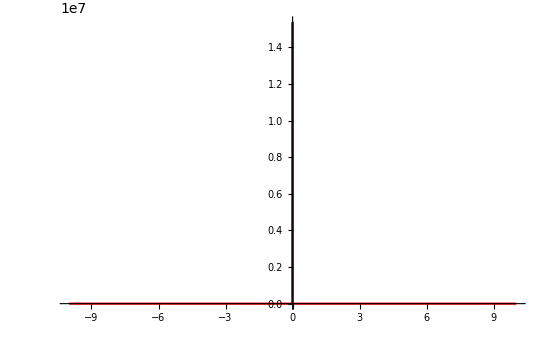

```mathematica
plot1=ListLinePlot[pdfzeta2,PlotStyle->Red,PlotRange->Full] (*You can use different plot range to see how it looks like*)
```

```mathematica
fun10=Interpolation[pdfzeta2,InterpolationOrder->1];
```

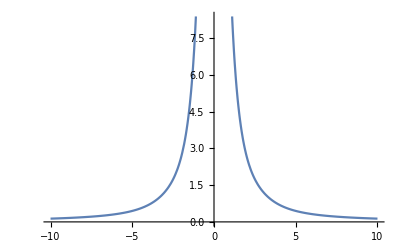

```mathematica
plot2=Plot[fun10[x],{x,-10,10},PlotRange->Automatic]
```

```mathematica
AreaPDF=(NIntegrate[fun10[z],{z,Min[points],Max[points]}]) (*To normalize the pdf*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.0387517}. NIntegrate obtained 77895.4 and 4866.66 for the integral and error estimates.

77895.4

```mathematica
pdfζphaseNormalized=Transpose[{points,pdfzeta/AreaPDF}];
```

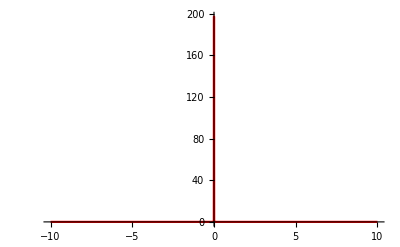

```mathematica
plot2=ListLinePlot[pdfζphaseNormalized,PlotStyle->Red,PlotRange->All] (*You can you use different plot range see how this function looks like*)
```

```mathematica
Meanζphase=Total[points*pdfzeta/AreaPDF] (*For a discrete pdf, this is how we derive expectation value- Σ Subscript[P, i] Subscript[ζ, i] , where Subscript[P, i] is the value of pdf at Subscript[ζ, i] . The expectation value is supposed to be zero, for some reason mathematica is giving a very small value*)
```

-3.03577×10^-18

```mathematica
stdevζphase=Sqrt[Total[(points-Meanζphase)^2*pdfzeta/AreaPDF]] (*This is the 1-sigma upper bound on zeta from the phase correction. The formula is Σ Subscript[P, i](Meanζ-Subscript[ζ, i])^2*)
```

0.539191

```mathematica
(*Now we are going to find bound on alpha_EDGB^2 from the selceted data that satisfies zeta<1. The reason of choosing this instead of square root of alpha_EDGB is that thisis proportional to ppE_beta. So we know that it's distribution is going to be Gaussian.*)
```

```mathematica
LogSqrtαPhase=Log[SqrtαEDGBphaseSelected^4] (*This is Log of sigma_(alpha^2)*)
```

{2.80248,3.70165,4.76956,3.36568,2.58768,4.31801,2.86279,2.73981,4.58271,2.97046,5.80019,2.44705,2.36796,2.55155,46845,2.19386,6.11602,2.14612,4.2719,3.46894,2.87685,3.45468,3.28,1.13134,3.44905,6.20047,3.21978,3.87642}
 |  |  |  |

```mathematica
𝒟logα=HistogramDistribution[LogSqrtαPhase]
```

DataDistribution[…]

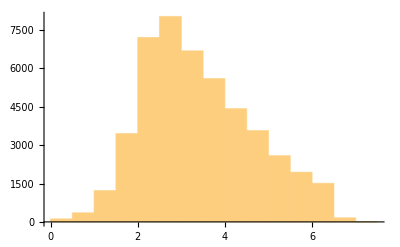

```mathematica
Histogram[LogSqrtαPhase]
```

```mathematica
func1=PDF[𝒟logα,LogSqrtαPhase] (*pdf of log(sigma_alphaEDGB^2)|log_sigma_alphaEDGB^2*)
```

{0.342635,0.239034,0.152244,0.285288,0.342635,0.188855,0.342635,0.342635,0.152244,0.342635,0.0829066,0.307561,0.307561,46846,0.307561,0.0643881,0.307561,0.188855,0.285288,0.342635,0.285288,0.285288,0.0522273,0.285288,0.0643881,0.285288,0.239034}
 |  |  |  |

```mathematica
func2=1/(√(2*π)*Exp[LogSqrtαPhase])*Exp[-x^2/(2Exp[2 LogSqrtαPhase])](*x is \[Zeta. and ζphaseAll is sigma_zeta from Fisher analysis of Overall dataset*)
```

{0.0241995 ⅇ^(-0.00183977 x^2),0.00984698 ⅇ^(-0.000304618 x^2),0.00338465 ⅇ^(-0.0000359897 x^2),0.0137788 ⅇ^(-0.000596451 x^2),0.0299981 ⅇ^(-0.00282707 x^2),46863,0.0126767 ⅇ^(-0.000504846 x^2),0.000809247 ⅇ^(-2.05737×10^-6 x^2),0.0159432 ⅇ^(-0.00079855 x^2),0.00826806 ⅇ^(-0.000214762 x^2)}
 |  |  |  |

```mathematica
func3=func1*func2
```

{0.0082916 ⅇ^(-0.00183977 x^2),0.00235376 ⅇ^(-0.000304618 x^2),0.000515295 ⅇ^(-0.0000359897 x^2),0.00393093 ⅇ^(-0.000596451 x^2),0.0102784 ⅇ^(-0.00282707 x^2),46863,0.00361649 ⅇ^(-0.000504846 x^2),0.0000521059 ⅇ^(-2.05737×10^-6 x^2),0.0045484 ⅇ^(-0.00079855 x^2),0.00197635 ⅇ^(-0.000214762 x^2)}
 |  |  |  |

```mathematica
ΔLogSqrtαPhase=Table[Abs[LogSqrtαPhase[[i+1]]-LogSqrtαPhase[[i]]],{i,1,Length[LogSqrtαPhase]-1}]
```

{0.899167,1.06791,1.40388,0.778,1.73033,1.45522,0.122976,1.8429,1.61225,2.82973,3.35314,0.0790819,0.183583,46845,1.73439,3.92216,3.96989,2.12578,0.802961,0.592087,0.577823,0.174674,2.14866,2.31771,2.75141,2.98068,0.656634}
 |  |  |  |

```mathematica
function5=Table[ΔLogSqrtαPhase[[i]]*func3[[i]],{i,1,Length[ΔLogSqrtαPhase]}]
```

{0.00745553 ⅇ^(-0.00183977 x^2),0.00251361 ⅇ^(-0.000304618 x^2),0.000723413 ⅇ^(-0.0000359897 x^2),0.00305826 ⅇ^(-0.000596451 x^2),0.017785 ⅇ^(-0.00282707 x^2),46862,0.0155787 ⅇ^(-0.0520352 x^2),0.00995046 ⅇ^(-0.000504846 x^2),0.000155311 ⅇ^(-2.05737×10^-6 x^2),0.00298664 ⅇ^(-0.00079855 x^2)}
 |  |  |  |

```mathematica
function5=Total[function5] (*This is the pdf of alpha_EDGB^2*)
```

0.00444267 ⅇ^(-0.483008 x^2)+0.00733614 ⅇ^(-0.473205 x^2)+0.00370568 ⅇ^(-0.426595 x^2)+0.00468619 ⅇ^(-0.425781 x^2)+0.00843587 ⅇ^(-0.425696 x^2)+46862+0.0000135372 ⅇ^(-4.98307×10^-7 x^2)+0.000010115 ⅇ^(-4.50047×10^-7 x^2)+0.0000121715 ⅇ^(-4.41789×10^-7 x^2)+9.65419×10^-9 ⅇ^(-4.00993×10^-7 x^2)
 |  |  |  |

```mathematica
function6[x_]=function5
```

0.00444267 ⅇ^(-0.483008 x^2)+0.00733614 ⅇ^(-0.473205 x^2)+0.00370568 ⅇ^(-0.426595 x^2)+0.00468619 ⅇ^(-0.425781 x^2)+0.00843587 ⅇ^(-0.425696 x^2)+46862+0.0000135372 ⅇ^(-4.98307×10^-7 x^2)+0.000010115 ⅇ^(-4.50047×10^-7 x^2)+0.0000121715 ⅇ^(-4.41789×10^-7 x^2)+9.65419×10^-9 ⅇ^(-4.00993×10^-7 x^2)
 |  |  |  |

```mathematica
Sample2= Table[10*i,{i,-100,100}]//N;
```

```mathematica
points2=Table[Sample2[[i]],{i,1,201}] ;(*These are the values of alpha_EDGB^2 that we are going to use for plotting the pdf*)
```

```mathematica
pdfα=Map[function6,points2] (*This is going to take about a minute*)
```

General::munfl: Exp[-483008.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-473205.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-426595.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0385934,0.040183,0.0418365,0.0435566,0.045346,0.0472077,0.0491447,0.0511601,0.0532574,0.05544,0.0577117,0.0600763,0.0625378,0.0651007,0.0677693,0.0705485,0.0734433,0.0764589,0.079601,0.0828755,0.0862886,0.089847,0.0935575,0.0974278,0.101466,0.105679,0.110078,0.114671,0.119469,0.124481,0.12972,0.135199,0.140929,0.146925,0.153202,0.159777,0.166666,0.173888,0.181463,0.189412,0.19776,0.206531,0.215751,0.225452,0.235664,0.246423,0.257767,0.269736,0.282377,0.295739,0.309876,0.32485,0.340725,0.357577,0.375486,0.394543,0.414849,0.436516,0.459672,0.484456,0.511029,0.539569,0.570277,0.603384,0.639147,0.677861,0.71986,0.765527,0.8153,0.869681,0.929251,0.994679,1.06675,1.14636,1.23458,1.33268,1.44214,1.56474,1.70262,1.85838,2.0352,2.23701,2.46878,2.73681,3.04925,3.41686,3.85402,4.38037,5.02322,5.82151,6.83231,8.14245,9.89015,12.3091,15.8278,21.318,30.7831,49.4426,92.6234,199.295,336.117,199.295,92.6234,49.4426,30.7831,21.318,15.8278,12.3091,9.89015,8.14245,6.83231,5.82151,5.02322,4.38037,3.85402,3.41686,3.04925,2.73681,2.46878,2.23701,2.0352,1.85838,1.70262,1.56474,1.44214,1.33268,1.23458,1.14636,1.06675,0.994679,0.929251,0.869681,0.8153,0.765527,0.71986,0.677861,0.639147,0.603384,0.570277,0.539569,0.511029,0.484456,0.459672,0.436516,0.414849,0.394543,0.375486,0.357577,0.340725,0.32485,0.309876,0.295739,0.282377,0.269736,0.257767,0.246423,0.235664,0.225452,0.215751,0.206531,0.19776,0.189412,0.181463,0.173888,0.166666,0.159777,0.153202,0.146925,0.140929,0.135199,0.12972,0.124481,0.119469,0.114671,0.110078,0.105679,0.101466,0.0974278,0.0935575,0.089847,0.0862886,0.0828755,0.079601,0.0764589,0.0734433,0.0705485,0.0677693,0.0651007,0.0625378,0.0600763,0.0577117,0.05544,0.0532574,0.0511601,0.0491447,0.0472077,0.045346,0.0435566,0.0418365,0.040183,0.0385934}

```mathematica
pdfα2=Transpose[{points2,pdfα}];
```

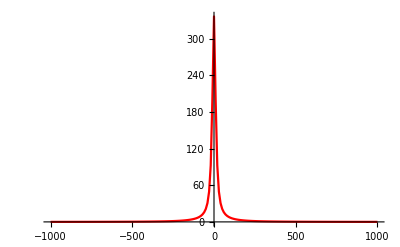

```mathematica
plot3=ListLinePlot[pdfα2,PlotStyle->Red,PlotRange->All]
```

```mathematica
function7=Interpolation[pdfα2,InterpolationOrder->1];
```

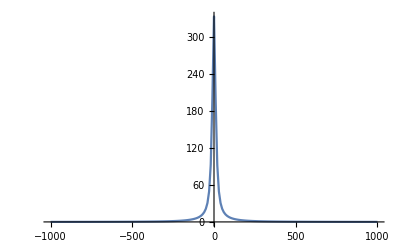

```mathematica
plot4=Plot[function7[x],{x,-1000,1000},PlotRange->All]
```

```mathematica
AreaPDFα=(NIntegrate[function7[z],{z,Min[points],Max[points]}]) (*To normalize the pdf*)
```

5354.11

```mathematica
pdfnormalizedα=Transpose[{points2,pdfα/AreaPDFα}];
```

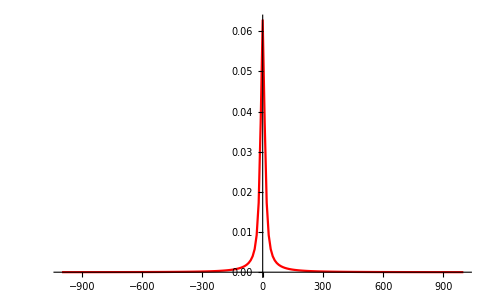

```mathematica
plot2=ListLinePlot[pdfnormalizedα,PlotStyle->Red,PlotRange->All]
```

```mathematica
Meanα=
Total[points2*pdfα/AreaPDFα] (*This is supposed to be zero*)
```

8.88178×10^-16

```mathematica
stdevα=Sqrt[Total[(points2-Meanα)^2*pdfα/AreaPDFα]] (*1-sigma upper bound on alpha_EDGB^2 *)
```

49.9274

```mathematica
√√stdevα (*Rough estimate of square root alpha_EDGB from phase correction*)
```

2.65818

## More accurate Integration for ζ

### 2D Gaussian, ζ samples

```mathematica
fun1Kent[x_,y_]=1/(√(2*π) Exp[y])*Exp[-x^2/(2Exp[2y])];
```

ζ sample

```mathematica
ζSampleLog=10^Range[-5,2,0.1];
```

Creating a table for fun1Kent[x,y] at each ζ sample for x

```mathematica
fun1TableLog[y_]=Table[{ζSampleLog[[i]],fun1Kent[ζSampleLog[[i]],y]},{i,1,Length[ζSampleLog]}];
```

### Creating an interpolation function for the Monte-Carlo probability distribution on σ_Σ

```mathematica
ζMC[x_]=ps1;
```

```mathematica
ζMC[-14.5]
ζMC[16.5]
```

0.

0.

ζ sample for creating an interpolation function for the MC prob distribution
Since ζ > 0, I only consider positive ζ

```mathematica
ζMCSample=Range[-14.5,16.5,1];
```

creating a table for the MC distribution at each sample ζ

```mathematica
ζMCTable=Table[{ζMCSample[[i]],ζMC[ζMCSample[[i]]]},{i,1,Length[ζMCSample]}];
```

creating an interpolation function

```mathematica
ζMCTableInterp=Interpolation[ζMCTable];
```

Plot

```mathematica
plotζMCTableInterp=Plot[ζMCTableInterp[x],{x,-14.5,16.5},PlotStyle->Blue,PlotLegends->{"Interpolation"}];
```

Comparison with the actual distribution

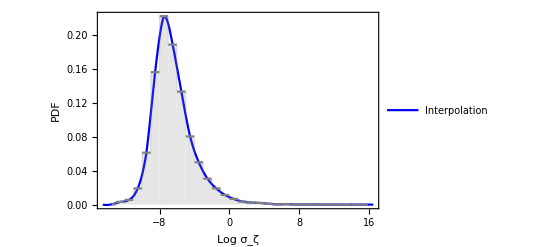

```mathematica
Show[plotζMCTableInterp,plottest2,Frame->True,FrameLabel->{"Log σ_ζ","PDF"}]
```

Nice agreement!

### Finding PDF for ζ

```mathematica
MaxLogζphase=Log[Max[ζphaseAll]]
MinLogζphase=Log[Min[ζphaseAll]]
```

15.8769

-13.4813

#### Raw Distribution

Creating a table for ∫ P(ζ|σ_Σ) P(σ_Σ) dσ_Σ for each sample ζ using NIntegrate

```mathematica
ζFinalPDFPhaseLog=Table[{fun1TableLog[y][[i,1]],NIntegrate[fun1TableLog[y][[i,2]]ζMCTableInterp[y],{y,MinLogζphase,MaxLogζphase}]},{i,1,Length[fun1TableLog[y]]}];
```

Comparison with Sharaban’s result (there’s a big difference between the two)

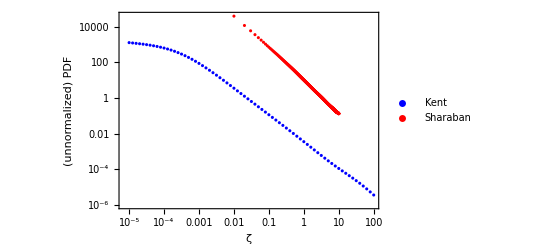

```mathematica
ListLogLogPlot[{ζFinalPDFPhaseLog,pdfzeta2},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"Kent","Sharaban"},FrameLabel->{"ζ","(unnormalized) PDF"}]
```

#### Normalized Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLog=Interpolation[ζFinalPDFPhaseLog];
```

Normalization

```mathematica
Normalization=NIntegrate[ζFinalPDFPhaseInterpLog[x],{x,10^-5,100}]
```

0.483797

Normalized distribution

```mathematica
ζFinalPDFPhaseLogNorm=Table[{ζFinalPDFPhaseLog[[i,1]],ζFinalPDFPhaseLog[[i,2]]/Normalization},{i,1,Length[ζFinalPDFPhaseLog]}];
```

Plot

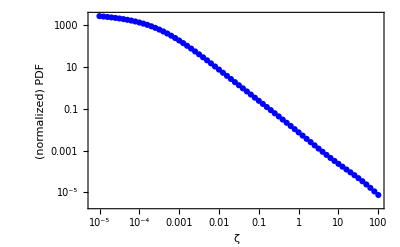

```mathematica
plotζFinalPDFPhaseLogNorm=ListLogLogPlot[{ζFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

#### Cumulative Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLogNorm=Interpolation[ζFinalPDFPhaseLogNorm];
```

Creating a table for cumulative distribution

```mathematica
ζFinalCDFPhaseNorm=Table[{ζSampleLog[[i]],NIntegrate[ζFinalPDFPhaseInterpLogNorm[x],{x,10^-5,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

Plot

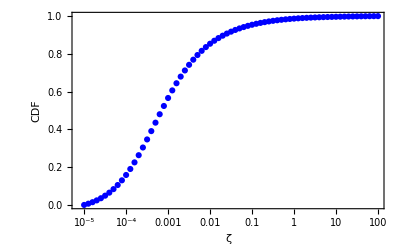

```mathematica
ListLogLinearPlot[ζFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

CDF nicely asymptotes to 1 (suggesting that ζ = 100 is large enough)

#### Finding 90% credible limit for ζ

Interpolation for CDF

```mathematica
ζFinalCDFPhaseNormInterp=Interpolation[ζFinalCDFPhaseNorm];
```

90% limit

```mathematica
FindRoot[ζFinalCDFPhaseNormInterp[x]==0.9,{x,0.02}]
```

{x→0.0213978}